## 1.

```mathematica
A=({{1, 1, 1, 1}, {-h1, 0, h2, h2+h3}, {1/2 h1^2, 0, 1/2 h2^2, 1/2(h2+h3)^2}, {-h1^3, 0, h2^3, (h2+h3)^3}});
b=({{0}, {0}, {1}, {0}});
ω = Inverse[A].b//FullSimplify//Flatten;
```

```mathematica
ω//MatrixForm
```

((2 (2 h2+h3))/(h1 (h1+h2) (h1+h2+h3))
(2 h1-4 h2-2 h3)/(h1 h2^2+h1 h2 h3)
(2 (-h1+h2+h3))/(h2 (h1+h2) h3)
(2 (h1-h2))/(h3 (h2+h3) (h1+h2+h3)))

```mathematica
h1^4 ω[[1]] + h2^4 ω[[3]] + (h2 + h3)^4 ω[[4]]//FullSimplify
```

-2 (h2 (h2+h3)-h1 (2 h2+h3))

## 6.

```mathematica
2/(3/2+h)-2 + h^2//FullSimplify
```

-2+h^2+4/(3+2 h)

```mathematica
sol=DSolve[{u''[x]+u[x]==-ⅇ^x,u'[0]-u[0]==0,u'[10]+u[10]==0},u[x],x]
```

{{u[x]→1/2 (ⅇ^10 Cos[10] Cos[x]-ⅇ^x Cos[x]^2+ⅇ^10 Cos[10] Sin[x]-ⅇ^x Sin[x]^2+ⅇ^10 Cos[x] Sin[10] Tan[10]+ⅇ^10 Sin[10] Sin[x] Tan[10])}}

```mathematica
y[x_]:=u[x]/.sol[[1]]
```

```mathematica
y[x]//FullSimplify
```

1/2 (-ⅇ^x+ⅇ^10 Sec[10] (Cos[x]+Sin[x]))

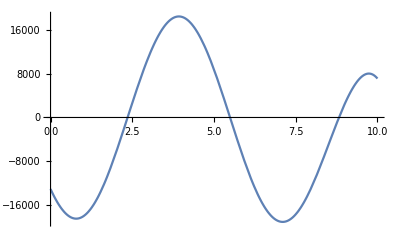

```mathematica
Plot[y[x],{x,0,10}]
```

## 8.

```mathematica
DSolve[{-u''[x]+u[x]==Sin[4π x],u[0]==u[1],u'[0]==u'[1]},u[x],x]
```

{{u[x]→Sin[4 π x]/(1+16 π^2)}}

```mathematica
Solve[{a == a*Cos[1] - b*Sin[1],b == a*Sin[1] + b*Cos[1]},{a,b}]
```

{{a→0,b→0}}

```mathematica
Solve[{b == a*Sin[1] + b*Cos[1]},{a}]
```

{{a→-(-b+b Cos[1]) Csc[1]}}

```mathematica
Sin[1]^2/(Cos[1]-1)+Cos[1]-1
```

-1+Cos[1]+Sin[1]^2/(-1+Cos[1])

```mathematica
N[-1+Cos[1]+Sin[1]^2/(-1+Cos[1])]
```

-2.

```mathematica
FullSimplify[(-Cos[1]^2+2Cos[1]-1-Sin[1]^2)/Sin[1]]
```

-2 Tan[1/2]

```mathematica
Tan[1/2]//N
```

0.546302